## Localised necking of a soft cylinder under surface tension

Prepared by Yibin Fu (y.fu@keele.ac.uk) for the advanced summer schools 2022 at CISM
For details, please refer to Fu, Jin & Goriely (JMPS, vol. 147, 2021)

### Governing equations

```mathematica
Gent97sub={W->Function[{x,y,z},-1/2 * (Jm) Log[1-(I1-3)/(Jm)]]};
```

```mathematica
F={{1/(√λz),0,0},{0,1/(√λz),0},{0,0,λz}}; Id={{1,0,0},{0,1,0},{0,0,1}};
Bt=(F.Transpose[F]);
μ=1; W0=wf[I1];   I10=Tr[Bt];
```

```mathematica
σ=(-pbar Id +2 wf'[I1] Bt)/.{I1->I10};
```

```mathematica
subp0=Solve[γ/b+σ[[1,1]]==0, pbar][[1]]
```

{pbar→(γ λz+2 b wf'[2/λz+λz^2])/(b λz)}

```mathematica
pbar=pbar/.subp0
```

(γ λz+2 b wf'[2/λz+λz^2])/(b λz)

```mathematica
phi=ϕ[R,z]; Subscript[r, R]=D[phi, R,z]/r1[R,z]; Subscript[r, z]=D[phi, z,z]/r1[R,z];Z=D[phi,R]/R;
(*obtained from FJG's eqn (2.9) *)
F11=Subscript[r, R]-Subscript[r, z] (D[Z,z])^-1 D[Z,R]; F13=Subscript[r, z] (D[Z,z])^-1; F31=-D[Z,R] (D[Z,z])^-1; F33=(D[Z,z])^-1;
F={{F11, 0, F13},{0, r1[R,z]/R, 0},{F31, 0, F33}};
```

```mathematica
I1=Tr[F.Transpose[F]]
```

r1[R,z]^2/R^2+R^2/((ϕ^(1,1)[R,z])^2)+(R^2 (ϕ^(0,2)[R,z])^2)/(r1[R,z]^2 (ϕ^(1,1)[R,z])^2)+(R^2 ((ϕ^(1,0)[R,z])/R^2-(ϕ^(2,0)[R,z])/R)^2)/((ϕ^(1,1)[R,z])^2)+((ϕ^(1,1)[R,z])/r1[R,z]-(R ϕ^(0,2)[R,z] (-(ϕ^(1,0)[R,z])/R^2+(ϕ^(2,0)[R,z])/R))/(r1[R,z] ϕ^(1,1)[R,z]))^2

```mathematica
a0=Numerator[Together[Simplify[I1]]]/.{r1[R,z]^2->(2 Derivative[0,1][ϕ][R,z]),r1[R,z]^4->(2 Derivative[0,1][ϕ][R,z])^2}
```

2 R^4 ϕ^(0,1)[R,z]+R^4 (ϕ^(0,2)[R,z])^2+2 ϕ^(0,1)[R,z] (ϕ^(1,0)[R,z])^2+(ϕ^(0,2)[R,z])^2 (ϕ^(1,0)[R,z])^2+4 (ϕ^(0,1)[R,z])^2 (ϕ^(1,1)[R,z])^2+2 R ϕ^(0,2)[R,z] ϕ^(1,0)[R,z] (ϕ^(1,1)[R,z])^2+R^2 (ϕ^(1,1)[R,z])^4-4 R ϕ^(0,1)[R,z] ϕ^(1,0)[R,z] ϕ^(2,0)[R,z]-2 R (ϕ^(0,2)[R,z])^2 ϕ^(1,0)[R,z] ϕ^(2,0)[R,z]-2 R^2 ϕ^(0,2)[R,z] (ϕ^(1,1)[R,z])^2 ϕ^(2,0)[R,z]+2 R^2 ϕ^(0,1)[R,z] (ϕ^(2,0)[R,z])^2+R^2 (ϕ^(0,2)[R,z])^2 (ϕ^(2,0)[R,z])^2

```mathematica
a1=Denominator[Together[Simplify[I1]]]/.{r1[R,z]^2->(2 Derivative[0,1][ϕ][R,z]),r1[R,z]^4->(2 Derivative[0,1][ϕ][R,z])^2}
```

2 R^2 ϕ^(0,1)[R,z] (ϕ^(1,1)[R,z])^2

```mathematica
I1=a0/a1
```

1/(2 R^2 ϕ^(0,1)[R,z] (ϕ^(1,1)[R,z])^2)(2 R^4 ϕ^(0,1)[R,z]+R^4 (ϕ^(0,2)[R,z])^2+2 ϕ^(0,1)[R,z] (ϕ^(1,0)[R,z])^2+(ϕ^(0,2)[R,z])^2 (ϕ^(1,0)[R,z])^2+4 (ϕ^(0,1)[R,z])^2 (ϕ^(1,1)[R,z])^2+2 R ϕ^(0,2)[R,z] ϕ^(1,0)[R,z] (ϕ^(1,1)[R,z])^2+R^2 (ϕ^(1,1)[R,z])^4-4 R ϕ^(0,1)[R,z] ϕ^(1,0)[R,z] ϕ^(2,0)[R,z]-2 R (ϕ^(0,2)[R,z])^2 ϕ^(1,0)[R,z] ϕ^(2,0)[R,z]-2 R^2 ϕ^(0,2)[R,z] (ϕ^(1,1)[R,z])^2 ϕ^(2,0)[R,z]+2 R^2 ϕ^(0,1)[R,z] (ϕ^(2,0)[R,z])^2+R^2 (ϕ^(0,2)[R,z])^2 (ϕ^(2,0)[R,z])^2)

```mathematica
check=(Derivative[1,1][ϕ][R,z])^2/(2 Derivative[0,1][ϕ][R,z])-(Derivative[0,2][ϕ][R,z])/(Derivative[0,1][ϕ][R,z])*(Derivative[2,0][ϕ][R,z]-(Derivative[1,0][ϕ][R,z])/R)+R^2/(Derivative[1,1][ϕ][R,z])^2(((Derivative[2,0][ϕ][R,z])/R-(Derivative[1,0][ϕ][R,z])/R^2)^2+1)*((Derivative[0,2][ϕ][R,z])^2/(2 Derivative[0,1][ϕ][R,z])+1)+(2 Derivative[0,1][ϕ][R,z])/R^2;
```

```mathematica
Simplify[I1/check]
```

1

```mathematica
subr1={Derivative[1,0][r1][R,z]->Subscript[r, R], Derivative[0,1][r1][R,z]->Subscript[r, z]};
```

```mathematica
Subscript[r, RR]=D[Subscript[r, R],R]/.subr1; Subscript[r, Rz]=D[Subscript[r, R],z]/.subr1;  Subscript[r, zz]=D[Subscript[r, z],z]/.subr1;
subr2={Derivative[1,0][r1][R,z]->Subscript[r, R], Derivative[0,1][r1][R,z]->Subscript[r, z], Derivative[2,0][r1][R,z]->Subscript[r, RR],Derivative[1,1][r1][R,z]->Subscript[r, Rz],Derivative[0,2][r1][R,z]->Subscript[r, zz]};
Subscript[r, RRR]=D[Subscript[r, RR],R]/.subr2;Subscript[r, RRz]=D[Subscript[r, RR],z]/.subr2;
Subscript[r, Rzz]=D[Subscript[r, Rz],z]/.subr2;Subscript[r, zzz]=D[Subscript[r, zz],z]/.subr2;
subr3={Derivative[1,0][r1][R,z]->Subscript[r, R], Derivative[0,1][r1][R,z]->Subscript[r, z], Derivative[2,0][r1][R,z]->Subscript[r, RR],Derivative[1,1][r1][R,z]->Subscript[r, Rz],Derivative[0,2][r1][R,z]->Subscript[r, zz],
Derivative[3,0][r1][R,z]->Subscript[r, RRR], Derivative[2,1][r1][R,z]->Subscript[r, RRz],Derivative[1,2][r1][R,z]->Subscript[r, Rzz], Derivative[0,3][r1][R,z]->Subscript[r, zzz]};
subrr={r1[R,z]^2->(2 Derivative[0,1][ϕ][R,z]),r1[R,z]^4->(2 Derivative[0,1][ϕ][R,z])^2,r1[R,z]^6->(2 Derivative[0,1][ϕ][R,z])^3};
```

```mathematica
Ue= wf[I1] Derivative[1,1][ϕ][R,z]; UsB= γ √(2 Derivative[0,1][ϕ][B,z]+(Derivative[0,2][ϕ][B,z])^2);
eqn=D[D[Ue,Derivative[2,0][ϕ][R,z]],R,R]+  D[D[Ue,Derivative[1,1][ϕ][R,z]],R,z]+D[D[Ue,Derivative[0,2][ϕ][R,z]],z,z]-D[D[Ue,Derivative[1,0][ϕ][R,z]],R]-D[D[Ue,Derivative[0,1][ϕ][R,z]],z];
eqn=R^2 r1[R,z]^6 (Derivative[1,1][ϕ][R,z])^5*Simplify[eqn/.subr3];
```

#### Solid cylinder

```mathematica
λz=λ; a=0;A=0;
```

```mathematica
eqn=eqn/.subrr;
```

```mathematica
bc1a=D[Ue,Derivative[1,0][ϕ][R,z]]-D[D[Ue,Derivative[2,0][ϕ][R,z]],R]-D[D[Ue,Derivative[1,1][ϕ][R,z]],z]-D[D[UsA,Derivative[0,2][ϕ][A,z]],z,z]+D[D[UsA,Derivative[0,1][ϕ][A,z]],z];
bc1b=D[Ue,Derivative[1,0][ϕ][R,z]]-D[D[Ue,Derivative[2,0][ϕ][R,z]],R]-D[D[Ue,Derivative[1,1][ϕ][R,z]],z]+D[D[UsB,Derivative[0,2][ϕ][B,z]],z,z]-D[D[UsB,Derivative[0,1][ϕ][B,z]],z];
```

```mathematica
bc1b=R r1[R,z]^4 (Derivative[1,1][ϕ][R,z])^4 Simplify[bc1b/.subr3]/.subrr;
```

```mathematica
bc2=r1[R,z]^2 (Derivative[1,1][ϕ][R,z])^2 Simplify[D[Ue,Derivative[2,0][ϕ][R,z]]/.subr3]/.subrr;
bc1saved=Numerator[Simplify[bc1b/.subr3]]/.subrr;
bc2saved=Numerator[ Simplify[D[Ue,Derivative[2,0][ϕ][R,z]]/.subr3]/.subrr];
```

### Linear analysis

```mathematica
lineqn=Coefficient[Series[eqn/.ϕ->Function[{R,z},(z R^2)/(2 λ)+1/2(a^2-A^2/λ) z+ϵ*R*f[R/√λ] ⅇ^(I k z)],{ϵ,0,1}],ϵ];
```

```mathematica
jj1=λ^10/(2 R^9) Simplify[lineqn /(ⅇ^(I k z))];
```

```mathematica
lineqn=jj1;
```

```mathematica
bc1=Simplify[Coefficient[Series[bc1b/.ϕ->Function[{R,z},(z R^2)/(2 λ)+1/2(a^2-A^2/λ) z+ϵ*R*f[R/√λ]  ⅇ^(I k z)],{ϵ,0,1}],ϵ]];
```

```mathematica
bc2=Simplify[Coefficient[Series[bc2/.ϕ->Function[{R,z},(z R^2)/(2 λ)+1/2(a^2-A^2/λ) z+ϵ*R*f[R/√λ]  ⅇ^(I k z)],{ϵ,0,1}],ϵ]];
```

```mathematica
bc1=bc1 B^3 λ^(15/2)/(ⅇ^(ⅈ k z) R^6);
```

```mathematica
bc2=Numerator[bc2]/(2 ⅇ^(ⅈ k z) R^2 wf'[(2+λ^3)/λ]);
```

```mathematica
Collect[(bc2/R^2)/.R->(√λ r),{f''[r], f'[r],f[r]}]
```

((-λ+k^2 r^2 λ) f[r])/(r^2 λ)+f'[r]/r+f''[r]

```mathematica
tem=Coefficient[bc1,Derivative[3][f][R/(√λ)]]
```

-2 B^3 R^3 λ wf'[(2+λ^3)/λ]

```mathematica
gg1=Collect[(bc1/tem)/.R->(√λ r)/.f[B/(√λ)]->f[r],{Derivative[3][f][r],f''[r], f'[r],f[r]}]
```

(2 f''[r])/r-(f'[r] (λ (λ+k^2 r^2 λ (2+λ^3)) wf'[(2+λ^3)/λ]+2 k^2 r^2 λ (-1+λ^3)^2 wf''[(2+λ^3)/λ]))/(r^2 λ^2 wf'[(2+λ^3)/λ])-(f[r] ((B k^2 r^3 γ (B^2 k^2-λ) λ^2)/((B^2/λ)^(3/2))+2 √λ (λ^2 (-1+k^2 r^2 λ^3) wf'[(2+λ^3)/λ]+2 k^2 r^2 λ (-1+λ^3)^2 wf''[(2+λ^3)/λ])))/(2 r^3 λ^(5/2) wf'[(2+λ^3)/λ])+f^(3)[r]

```mathematica
gg2=Simplify[r^2 Coefficient[gg1,f'[r]] ]
```

-1-k^2 r^2 (2+λ^3)-(2 k^2 r^2 (-1+λ^3)^2 wf''[(2+λ^3)/λ])/(λ wf'[(2+λ^3)/λ])

```mathematica
gg3=gg2/.{wf''[(2+λ^3)/λ]->wf'[(2+λ^3)/λ] Subscript[ω, 1]}
```

-1-k^2 r^2 (2+λ^3)-(2 k^2 r^2 (-1+λ^3)^2 ω_1)/λ

```mathematica
gg2=Simplify[r^3 Coefficient[gg1,f[r]] /.{wf''[(2+λ^3)/λ]->wf'[(2+λ^3)/λ] Subscript[ω, 1]}/.B->(√λ r)/.wf'[(2+λ^3)/λ]->Subscript[w, d],r>0]
```

1-k^2 r^2 λ^3-(k^2 r (-1+k^2 r^2) γ λ)/(2 w_d)-(2 k^2 r^2 (-1+λ^3)^2 ω_1)/λ

```mathematica
co4=Coefficient[lineqn,Derivative[4][f][R/√λ]]
```

R^4 λ wf'[(2+λ^3)/λ]

```mathematica
co3=Simplify[Coefficient[lineqn,Derivative[3][f][R/√λ]]/co4]
```

(2 √λ)/R

```mathematica
R2=A^2+λ (r^2-a^2);R4=R2*R2;R6=R2^3;
```

```mathematica
tt1=Simplify[Numerator[Simplify[Coefficient[lineqn,Derivative[2][f][R/√λ]]/co4]]/.R^2->(A^2+λ (r^2-a^2))]
```

-(3 λ)/R^2-k^2 (1+λ^3)-(2 k^2 (-1+λ^3)^2 wf''[(2+λ^3)/λ])/(λ wf'[(2+λ^3)/λ])

```mathematica
tt2=Simplify[Denominator[Simplify[Coefficient[lineqn,Derivative[2][f][R/√λ]]/co4]]/.(R^2-A^2)->λ (r^2-a^2)]
```

1

```mathematica
co2=tt1/tt2
```

-(3 λ)/R^2-k^2 (1+λ^3)-(2 k^2 (-1+λ^3)^2 wf''[(2+λ^3)/λ])/(λ wf'[(2+λ^3)/λ])

```mathematica
co1=Simplify[Coefficient[lineqn,Derivative[1][f][R/√λ]]/co4]
```

(3 λ^2-k^2 R^2 λ (1+λ^3)-(2 k^2 R^2 (-1+λ^3)^2 wf''[(2+λ^3)/λ])/wf'[(2+λ^3)/λ])/(R^3 √λ)

```mathematica
top=Simplify[Numerator[co1/.{R^6->R6, R^4->R4, R^2->R2}]]
```

λ (3 λ-k^2 r^2 λ (1+λ^3)-(2 k^2 r^2 (-1+λ^3)^2 wf''[(2+λ^3)/λ])/wf'[(2+λ^3)/λ])

```mathematica
bot=Simplify[Denominator[co1/.{R^6->R6, R^4->R4, R^2->R2}]]
```

R^3 √λ

```mathematica
co1=top/bot
```

(√λ (3 λ-k^2 r^2 λ (1+λ^3)-(2 k^2 r^2 (-1+λ^3)^2 wf''[(2+λ^3)/λ])/wf'[(2+λ^3)/λ]))/R^3

```mathematica
co0=Simplify[Coefficient[lineqn,f[R/√λ]]/co4]
```

-(3 λ^2)/R^4+k^4 λ^3+(k^2 λ (1+λ^3))/R^2+(2 k^2 (-1+λ^3)^2 wf''[(2+λ^3)/λ])/(R^2 wf'[(2+λ^3)/λ])

```mathematica
Numerator[co0]
```

-(3 λ^2)/R^4+k^4 λ^3+(k^2 λ (1+λ^3))/R^2+(2 k^2 (-1+λ^3)^2 wf''[(2+λ^3)/λ])/(R^2 wf'[(2+λ^3)/λ])

```mathematica
top=Simplify[Numerator[co0/.{R^6->R6, R^4->R4, R^2->R2}]];
bot=Simplify[Denominator[co0/.{R^6->R6, R^4->R4, R^2->R2}]];
co0=top/bot;
```

```mathematica
R=√λ r;eqnn=Simplify[Derivative[4][f][r]+co3 Derivative[3][f][r] +co2 Derivative[2][f][r]+co1 Derivative[1][f][r]+co0 f[r]]
```

(f'[r] (3 λ-k^2 r^2 λ (1+λ^3)-(2 k^2 r^2 (-1+λ^3)^2 wf''[(2+λ^3)/λ])/wf'[(2+λ^3)/λ]))/(r^3 λ)+f''[r] (-3/r^2-k^2 (1+λ^3)-(2 k^2 (-1+λ^3)^2 wf''[(2+λ^3)/λ])/(λ wf'[(2+λ^3)/λ]))+f[r] (-3/r^4+k^4 λ^3+(k^2 (1+λ^3))/r^2+(2 k^2 (-1+λ^3)^2 wf''[(2+λ^3)/λ])/(r^2 λ wf'[(2+λ^3)/λ]))+(2 f^(3)[r])/r+f^(4)[r]

```mathematica
hh1=Collect[eqnn,{Derivative[4][f][r], Derivative[3][f][r],Derivative[2][f][r],f'[r],  f[r]}]
```

(f'[r] (3 λ-k^2 r^2 λ (1+λ^3)-(2 k^2 r^2 (-1+λ^3)^2 wf''[(2+λ^3)/λ])/wf'[(2+λ^3)/λ]))/(r^3 λ)+f''[r] (-3/r^2-k^2 (1+λ^3)-(2 k^2 (-1+λ^3)^2 wf''[(2+λ^3)/λ])/(λ wf'[(2+λ^3)/λ]))+f[r] (-3/r^4+k^4 λ^3+(k^2 (1+λ^3))/r^2+(2 k^2 (-1+λ^3)^2 wf''[(2+λ^3)/λ])/(r^2 λ wf'[(2+λ^3)/λ]))+(2 f^(3)[r])/r+f^(4)[r]

```mathematica
Collect[Coefficient[hh1, f''[r]],r]
```

-3/r^2-k^2 (1+λ^3)-(2 k^2 (-1+λ^3)^2 wf''[(2+λ^3)/λ])/(λ wf'[(2+λ^3)/λ])

#### Factorise the fourth order ODE

```mathematica
g[r_]=f''[r]+1/r f'[r]-(1/r^2+k^2 q1s) f[r];  (*q1s=Subscript[q, 1]^2*)
hh=Simplify[g''[r]+1/r g'[r]-(1/r^2+k^2 q2s) g[r]];
```

```mathematica
gg1=Collect[hh, {Derivative[4][f][r], Derivative[3][f][r],Derivative[2][f][r],f'[r],  f[r]}]
```

((-3+k^2 (q1s+q2s) r^2+k^4 q1s q2s r^4) f[r])/r^4-((-3+k^2 (q1s+q2s) r^2) f'[r])/r^3-((3+k^2 (q1s+q2s) r^2) f''[r])/r^2+(2 f^(3)[r])/r+f^(4)[r]

```mathematica
tem1=Collect[Coefficient[hh1, f''[r]]-Coefficient[gg1, f''[r]],r]
```

k^2 (q1s+q2s)-k^2 (1+λ^3)-(2 k^2 (-1+λ^3)^2 wf''[(2+λ^3)/λ])/(λ wf'[(2+λ^3)/λ])

```mathematica
q2s=Simplify[ q2s/.Solve[{tem1==0}, q2s][[1]]]
```

1-q1s+λ^3+(2 (-1+λ^3)^2 wf''[(2+λ^3)/λ])/(λ wf'[(2+λ^3)/λ])

```mathematica
tem1=Simplify[Collect[Coefficient[hh1, f'[r]]-Coefficient[gg1, f'[r]],r]]
```

0

```mathematica
tem2=Simplify[Collect[Coefficient[hh1, f[r]]-Coefficient[gg1, f[r]],r]]
```

k^4 (q1s^2+λ^3-q1s (1+λ^3)-(2 q1s (-1+λ^3)^2 wf''[(2+λ^3)/λ])/(λ wf'[(2+λ^3)/λ]))

```mathematica
subω1=Solve[tem2==0,q1s][[1]]
```

{q1s→1/(2 λ wf'[(2+λ^3)/λ])(λ wf'[(2+λ^3)/λ]+λ^4 wf'[(2+λ^3)/λ]+2 wf''[(2+λ^3)/λ]-4 λ^3 wf''[(2+λ^3)/λ]+2 λ^6 wf''[(2+λ^3)/λ]-√(-4 λ^5 wf'[(2+λ^3)/λ]^2+(-λ wf'[(2+λ^3)/λ]-λ^4 wf'[(2+λ^3)/λ]-2 wf''[(2+λ^3)/λ]+4 λ^3 wf''[(2+λ^3)/λ]-2 λ^6 wf''[(2+λ^3)/λ])^2))}

```mathematica
q1s=q1s/.subω1
```

1/(2 λ wf'[(2+λ^3)/λ])(λ wf'[(2+λ^3)/λ]+λ^4 wf'[(2+λ^3)/λ]+2 wf''[(2+λ^3)/λ]-4 λ^3 wf''[(2+λ^3)/λ]+2 λ^6 wf''[(2+λ^3)/λ]-√(-4 λ^5 wf'[(2+λ^3)/λ]^2+(-λ wf'[(2+λ^3)/λ]-λ^4 wf'[(2+λ^3)/λ]-2 wf''[(2+λ^3)/λ]+4 λ^3 wf''[(2+λ^3)/λ]-2 λ^6 wf''[(2+λ^3)/λ])^2))

```mathematica
q1s=Simplify[(Numerator[q1s]/.{wf'[(2+λ^3)/λ]->Subscript[w, d],  wf''[(2+λ^3)/λ]->Subscript[w, dd]})/Denominator[q1s]/.{wf'[(2+λ^3)/λ]->Subscript[w, d],  wf''[(2+λ^3)/λ]->Subscript[w, dd]}]
```

(λ w_d+λ^4 w_d+2 w_dd-4 λ^3 w_dd+2 λ^6 w_dd-√(-4 λ^5 w_d^2+((λ+λ^4) w_d+2 (-1+λ^3)^2 w_dd)^2))/(2 λ w_d)

```mathematica
q1s=Simplify[q1s/.{Subscript[w, dd]->(Subscript[w, d] Subscript[ω, 1])}, Subscript[w, d]>0]
```

(λ+λ^4+2 ω_1-4 λ^3 ω_1+2 λ^6 ω_1-√(-4 λ^5+(λ+λ^4+2 (-1+λ^3)^2 ω_1)^2))/(2 λ)

```mathematica
q2s=Simplify[q2s/.{wf''[(2+λ^3)/λ]->wf'[(2+λ^3)/λ] Subscript[ω, 1]}]
```

(λ+λ^4+2 ω_1-4 λ^3 ω_1+2 λ^6 ω_1+√(-4 λ^5+(λ+λ^4+2 (-1+λ^3)^2 ω_1)^2))/(2 λ)

```mathematica
cc1=Coefficient[bc1, Derivative[3][f][r]];
```

```mathematica
cc2=Coefficient[bc2, Derivative[2][f][r]];
```

```mathematica
bc1=Simplify[Collect[Simplify[bc1/cc1], {Derivative[3][f][r],Derivative[2][f][r],f'[r],  f[r]}], {B>0,λ>0}]
```

((1-k^2 r^2 λ^3) f[r])/r^3-f'[r]/r^2-k^2 (2+λ^3) f'[r]-(k^2 γ (B^2 k^2-λ) λ f[B/(√λ)])/(2 B^2 wf'[(2+λ^3)/λ])+(2 f''[r])/r-(2 k^2 (-1+λ^3)^2 f[r] wf''[(2+λ^3)/λ])/(r λ wf'[(2+λ^3)/λ])-(2 k^2 (-1+λ^3)^2 f'[r] wf''[(2+λ^3)/λ])/(λ wf'[(2+λ^3)/λ])+f^(3)[r]

```mathematica
bc1=Simplify[bc1/.B->(√λ r)]
```

-((1+k^2 r^2 (2+λ^3)) f'[r])/r^2+(2 f''[r])/r-(2 k^2 (-1+λ^3)^2 f'[r] wf''[(2+λ^3)/λ])/(λ wf'[(2+λ^3)/λ])+(f[r] (2-2 k^2 r^2 λ^3-(k^2 r ((-1+k^2 r^2) γ λ^2+4 r (-1+λ^3)^2 wf''[(2+λ^3)/λ]))/(λ wf'[(2+λ^3)/λ])))/(2 r^3)+f^(3)[r]

```mathematica
bc1=Simplify[bc1/.{wf''[(2+λ^3)/λ]->wf'[(2+λ^3)/λ] Subscript[ω, 1]}/.{wf'[(2+λ^3)/λ]->Subscript[w, d],  wf''[(2+λ^3)/λ]->Subscript[w, dd]}]
```

(f[r] (2-2 k^2 r^2 λ^3-(k^2 r (-1+k^2 r^2) γ λ)/w_d-(4 k^2 r^2 (-1+λ^3)^2 ω_1)/λ))/(2 r^3)-((1+k^2 r^2 (2+λ^3)) f'[r])/r^2-(2 k^2 (-1+λ^3)^2 ω_1 f'[r])/λ+(2 f''[r])/r+f^(3)[r]

```mathematica
bc2= Collect[bc2/cc2, {Derivative[3][f][r],Derivative[2][f][r],f'[r],  f[r]}]
```

((-λ+k^2 r^2 λ) f[r])/(r^2 λ)+f'[r]/r+f''[r]

```mathematica
(* g[r_]=f''[r]+1/r f'[r]-(1/r^2+ω1 k^2 λ^3) f[r];
hh=Simplify[g''[r]+1/r g'[r]-(1/r^2+ω3 k^2 ) g[r]];*)
```

```mathematica
(* q1=λ^(3/2) √ω1;q2= √ω3;  ω1=ω1s, ω3=ω3s *) f[r_]=BesselI[1, k r q1]/BesselI[1, k r0 q1]+β BesselI[1, k r q2]/BesselI[1, k r0 q2];
```

```mathematica
subB=Solve[Simplify[bc2/.r->r0]==0, β][[1]]
```

{β→(-1-q1^2)/(1+q2^2)}

```mathematica
subb={BesselI[2,k q1 r0]->(BesselI[0,k q1 r0]-(2/(k q1 r0)) BesselI[1,k q1 r0]),BesselI[2,k q2 r0]->(BesselI[0,k q2 r0]-(2/(k q2 r0)) BesselI[1,k q2 r0]), BesselI[3,k q1 r0]->(BesselI[1,k q1 r0]-(4/(k q1 r0)) BesselI[2,k q1 r0]),BesselI[3,k q2 r0]->( BesselI[1,k q2 r0]-(4/(k q2 r0)) BesselI[2,k q2 r0])};
```

```mathematica
bbc=-(1+q1s)/(1+q2s);
```

```mathematica
q1s
```

(λ+λ^4+2 ω_1-4 λ^3 ω_1+2 λ^6 ω_1-√(-4 λ^5+(λ+λ^4+2 (-1+λ^3)^2 ω_1)^2))/(2 λ)

```mathematica
wdGent=wf'[(2+λ^3)/λ]/.wf->Function[x, -1/2 Subscript[J, m] Log[1-(x-3)/Subscript[J, m]]];wddGent=wf''[(2+λ^3)/λ]/.wf->Function[x, -1/2 Subscript[J, m] Log[1-(x-3)/Subscript[J, m]]];
```

```mathematica
subGent={wd->wdGent, wdd->wddGent,Subscript[ω, 1]->wddGent/wdGent, Subscript[w, d]->wdGent };
```

```mathematica
(* q1=λ^(3/2) √ω1;q2= √ω3;  ω1=ω1s, ω2=ω2s *)
```

```mathematica
bif=Simplify[bc1/.r->r0]/.β->bbc/.r0->B/λ^(1/2);
```

```mathematica
bifGent=bc1/.r->r0/.β->bbc/.r0->B/λ^(1/2)/.{q1->Sqrt[q1s], q2->Sqrt[q2s]}/.subGent;
```

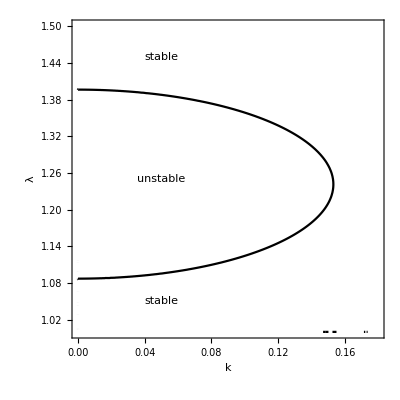

```mathematica
ContourPlot[(bifGent/.{B->1, Subscript[J, m]->97.2, γ->5.8})==0, {k,0,0.18},{λ,1, 1.5},WorkingPrecision->60,MaxRecursion->5,FrameLabel->{Style["k",FontSize->20,FontFamily->"Times New Roman"],Style["λ",FontSize->20,FontFamily->"Times New Roman"]},ContourStyle->{{PointSize[0.015], {Black,Solid}}}, TicksStyle->Directive[Black,12],BaseStyle->{FontSize->14},Epilog->{Text[Style["unstable",Medium],{0.05,1.25}],Text[Style["stable",Medium],{0.05,1.05}],Text[Style["stable",Medium],{0.05,1.45}]}]
```

```mathematica
temp=bifGent/.{B->1, Subscript[J, m]->97.2, γ->5.8};
```

#### Determine the point where dk/dλ=0. We differentiate temp[k[λ],λ]=0 implicitly w.r.t. λ and then set k’[λ]=0

```mathematica
dtemp=D[temp/.k->h[λ],λ]/.{h'[λ]->0,h[λ]->k};
subf=FindRoot[{temp==0,dtemp==0},{k,0.153},{λ,1.23}]
```

{k→0.153223,λ→1.24125}

```mathematica
data1={{k,λ}/.subf}
```

{{0.153223,1.24125}}

```mathematica
λupper=λ/.FindRoot[(temp/.k->0.00001)==0,{λ,1.4}]
```

1.39614

```mathematica
λlower=λ/.FindRoot[(temp/.k->0.00001)==0,{λ,1.08}]
```

1.08703

```mathematica
(* guess=1.2412497727821614*0.99;
Do[kk=0.15322325975298257-0.15322325975298257*i/200; guess=λ/.FindRoot[(temp/.k->kk)==0,{λ,guess}]; data1=Append[data1,{kk,guess}], {i,1,199}]; 

data2={};
guess=1.2412497727821614*1.01;
Do[kk=0.15322325975298257-0.15322325975298257*i/200; guess=λ/.FindRoot[(temp/.k->kk)==0,{λ,guess}]; data2=Append[data2,{kk,guess}], {i,1,199}]; 

data10=Join[Reverse[data2],data1]*)
```

```mathematica
(*The Do loop above produce the following data10 *)
```

```mathematica
data10={{0.0007661162987649128,1.3961449788057232},{0.0015322325975298257,1.396139173256502},{0.0022983488962947385,1.3961294981120935},{0.0030644651950596513,1.3961159521018491},{0.003830581493824564,1.39609853484828},{0.004596697792589477,1.3960772441248626},{0.00536281409135439,1.3960520786346617},{0.006128930390119303,1.3960230365036308},{0.0068950466888842155,1.395990115457851},{0.007661162987649128,1.3959533130398767},{0.008427279286414041,1.3959126263749653},{0.009193395585178954,1.3958680524680698},{0.009959511883943867,1.3958195879395205},{0.01072562818270878,1.3957672290941403},{0.011491744481473692,1.3957109719398708},{0.012257860780238605,1.3956508122040403},{0.013023977079003518,1.3955867453304143},{0.013790093377768431,1.3955187663901076},{0.014556209676533344,1.3954468702097131},{0.015322325975298257,1.3953710512658677},{0.01608844227406317,1.3952913037515666},{0.016854558572828082,1.3952076215228537},{0.017620674871592995,1.3951199981527471},{0.018386791170357908,1.3950284268498687},{0.01915290746912282,1.39493290053864},{0.019919023767887734,1.3948334118004457},{0.020685140066652646,1.3947299528944823},{0.02145125636541756,1.3946225157525263},{0.022217372664182472,1.3945110919763204},{0.022983488962947385,1.3943956728153302},{0.023749605261712298,1.3942762491960963},{0.02451572156047721,1.3941528116909658},{0.025281837859242123,1.3940253505285567},{0.026047954158007036,1.3938938555923108},{0.02681407045677195,1.3937583163920808},{0.027580186755536862,1.393618722097483},{0.02834630305430179,1.393475061495495},{0.029112419353066674,1.3933273230228633},{0.029878535651831586,1.3931754947270543},{0.030644651950596513,1.393019564288733},{0.031410768249361426,1.3928595189862474},{0.03217688454812634,1.3926953457312627},{0.03294300084689125,1.392527031014762},{0.033709117145656164,1.3923545609549037},{0.03447523344442108,1.392177921239692},{0.03524134974318599,1.391997097152903},{0.0360074660419509,1.391812073559667},{0.036773582340715816,1.3916228348936053},{0.03753969863948073,1.391429365159391},{0.03830581493824564,1.3912316479171922},{0.039071931237010554,1.3910296662771924},{0.03983804753577547,1.3908234029037798},{0.04060416383454038,1.3906128399853501},{0.04137028013330529,1.390397959241311},{0.042136396432070206,1.39017874191347},{0.04290251273083512,1.3899551687485499},{0.04366862902960003,1.3897272199960402},{0.044434745328364944,1.3894948753997023},{0.04520086162712986,1.3892581141796898},{0.04596697792589477,1.3890169150297456},{0.046733094224659696,1.3887712561016619},{0.04749921052342461,1.3885211149994992},{0.048265326822189494,1.388266468765697},{0.04903144312095441,1.3880072938655865},{0.049797559419719334,1.387743566178338},{0.05056367571848425,1.3874752609875196},{0.05132979201724916,1.3872023529632334},{0.05209590831601407,1.3869248161500993},{0.052862024614778985,1.3866426239508938},{0.0536281409135439,1.3863557491199787},{0.05439425721230881,1.386064163736213},{0.055160373511073724,1.385767839197945},{0.055926489809838636,1.3854667461994237},{0.05669260610860355,1.3851608547165406},{0.05745872240736846,1.384850133992236},{0.058224838706133375,1.3845345525142407},{0.05899095500489829,1.3842140779951413},{0.0597570713036632,1.3838886773589048},{0.06052318760242811,1.3835583167138197},{0.061289303901193026,1.383222961339904},{0.06205542019995794,1.382882575654962},{0.06282153649872285,1.3825371232005195},{0.06358765279748776,1.3821865666190323},{0.06435376909625268,1.3818308676250832},{0.06511988539501759,1.3814699869773617},{0.06588600169378252,1.3811038844613552},{0.06665211799254743,1.3807325188550907},{0.06741823429131232,1.3803558478980675},{0.06818435059007723,1.3799738282692535},{0.06895046688884215,1.3795864155483781},{0.06971658318760707,1.3791935641900057},{0.07048269948637198,1.3787952274830857},{0.0712488157851369,1.3783913575214806},{0.0720149320839018,1.377981905163911},{0.07278104838266672,1.3775668199963642},{0.07354716468143163,1.3771460502927857},{0.07431328098019654,1.3767195429729346},{0.07507939727896146,1.3762872435601279},{0.07584551357772637,1.3758490961329155},{0.07661162987649128,1.375405043280758},{0.0773777461752562,1.37495502605293},{0.07814386247402111,1.3744989839060753},{0.07890997877278602,1.3740368546507604},{0.07967609507155093,1.3735685743964992},{0.08044221137031585,1.3730940774880454},{0.08120832766908076,1.3726132964472977},{0.08197444396784567,1.3721261619050324},{0.08274056026661059,1.3716326025346424},{0.0835066765653755,1.3711325449796046},{0.08427279286414041,1.3706259137777643},{0.08503890916290532,1.370112631283094},{0.08580502546167024,1.3695926175820519},{0.08657114176043515,1.3690657904062966},{0.08733725805920006,1.3685320650413761},{0.08810337435796498,1.3679913542300128},{0.08886949065672989,1.3674435680705423},{0.0896356069554948,1.3668886139085599},{0.09040172325425971,1.3663263962265961},{0.09116783955302463,1.3657568165215037},{0.09193395585178954,1.3651797731833482},{0.09270007215055445,1.3645951613570635},{0.09346618844931937,1.3640028728078237},{0.09423230474808428,1.3634027957681827},{0.09499842104684919,1.3627948147842945},{0.0957645373456141,1.3621788105469865},{0.09653065364437902,1.361554659717866},{0.09729676994314393,1.360922234740895},{0.09806288624190884,1.3602814036449942},{0.09882900254067375,1.3596320298327225},{0.09959511883943867,1.3589739718562723},{0.10036123513820358,1.3583070831783277},{0.1011273514369685,1.3576312119205398},{0.1018934677357334,1.3569462005907498},{0.10265958403449832,1.356251885792623},{0.10342570033326323,1.3555480979225434},{0.10419181663202814,1.3548346608345914},{0.10495793293079306,1.3541113914894245},{0.10572404922955797,1.3533780995773637},{0.10649016552832288,1.3526345871116126},{0.1072562818270878,1.3518806479932366},{0.10802239812585271,1.3511160675438907},{0.10878851442461762,1.3503406220027674},{0.10955463072338253,1.3495540779819244},{0.11032074702214745,1.3487561918840525},{0.11108686332091236,1.3479467092682433},{0.11185297961967727,1.3471253641665288},{0.11261909591844219,1.3462918783451143},{0.1133852122172071,1.345445960498677},{0.11415132851597201,1.3445873053775086},{0.11491744481473692,1.3437155928385216},{0.11568356111350184,1.3428304868104433},{0.11644967741226675,1.3419316341610046},{0.11721579371103166,1.3410186634635195},{0.11798191000979658,1.3400911836388685},{0.11874802630856149,1.3391487824715316},{0.1195141426073264,1.3381910249705802},{0.12028025890609131,1.3372174515681312},{0.12104637520485623,1.3362275761243774},{0.12181249150362114,1.3352208837247188},{0.12257860780238605,1.3341968282273384},{0.12334472410115097,1.333154829540814},{0.12411084039991588,1.3320942705835719},{0.12487695669868079,1.3310144938827226},{0.1256430729974457,1.3299147977588313},{0.12640918929621062,1.328794432033787},{0.12717530559497553,1.3276525931818028},{0.12794142189374044,1.326488418836848},{0.12870753819250536,1.3253009815532164},{0.12947365449127027,1.3240892816761398},{0.13023977079003518,1.3228522391820552},{0.1310058870888001,1.3215886842785214},{0.131772003387565,1.3202973465477286},{0.13253811968632992,1.3189768423260422},{0.13330423598509483,1.3176256599704177},{0.13407035228385975,1.3162421425570205},{0.13483646858262466,1.3148244674379377},{0.13560258488138957,1.313370621936787},{0.13636870118015448,1.3118783742435494},{0.1371348174789194,1.3103452383001883},{0.1379009337776843,1.308768431079126},{0.13866705007644922,1.3071448201443876},{0.13943316637521413,1.3054708586352566},{0.14019928267397905,1.3037425037809647},{0.14096539897274396,1.3019551135280363},{0.14173151527150887,1.300103313632555},{0.1424976315702738,1.2981808241849062},{0.1432637478690387,1.2961802293013236},{0.1440298641678036,1.2940926654009717},{0.14479598046656852,1.2919073898263305},{0.14556209676533344,1.2896111683040732},{0.14632821306409835,1.2871873784857912},{0.14709432936286326,1.2846146497955186},{0.14786044566162818,1.281864707440548},{0.1486265619603931,1.2788987640877654},{0.149392678259158,1.275661046574267},{0.15015879455792291,1.2720660603635132},{0.15092491085668783,1.2679700668053002},{0.15169102715545274,1.2630931580039901},{0.15245714345421765,1.2567136746178136},{0.15322325975298257,1.2412497727821614},{0.15245714345421765,1.2257924037213395},{0.15169102715545274,1.2194194310810038},{0.15092491085668783,1.214549010838929},{0.15015879455792291,1.2104594834940958},{0.149392678259158,1.206870940992573},{0.1486265619603931,1.2036396445252742},{0.14786044566162818,1.2006800994002411},{0.14709432936286326,1.1979365322992532},{0.14632821306409835,1.1953701557345733},{0.14556209676533344,1.1929526947573157},{0.14479598046656852,1.1906627786391555},{0.1440298641678036,1.188483784878477},{0.1432637478690387,1.1864024790503365},{0.1424976315702738,1.1844081183457855},{0.14173151527150887,1.1824918390332009},{0.14096539897274396,1.1806462250793264},{0.14019928267397905,1.1788649964248066},{0.13943316637521413,1.1771427786793118},{0.13866705007644922,1.1754749296398705},{0.1379009337776843,1.1738574063909353},{0.1371348174789194,1.1722866619245509},{0.13636870118015448,1.1707595636596912},{0.13560258488138957,1.1692733284243493},{0.13483646858262466,1.1678254700180903},{0.13407035228385975,1.1664137564866415},{0.13330423598509483,1.1650361750112799},{0.13253811968632992,1.1636909028050686},{0.131772003387565,1.1623762828008364},{0.1310058870888001,1.1610908032177314},{0.13023977079003518,1.1598330802526091},{0.12947365449127027,1.1586018433485135},{0.12870753819250536,1.1573959225766302},{0.12794142189374044,1.1562142377768598},{0.12717530559497553,1.1550557891577367},{0.12640918929621062,1.1539196491388677},{0.1256430729974457,1.152804955219728},{0.12487695669868079,1.1517109037409272},{0.12411084039991588,1.1506367443918386},{0.12334472410115097,1.1495817753612199},{0.12257860780238605,1.148545339043759},{0.12181249150362114,1.1475268182294673},{0.12104637520485623,1.146525632694977},{0.12028025890609131,1.1455412361713246},{0.1195141426073264,1.1445731136159518},{0.11874802630856149,1.1436207787587032},{0.11798191000979658,1.1426837719089402},{0.11721579371103166,1.1417616579491043},{0.11644967741226675,1.1408540245366043},{0.11568356111350184,1.1399604804701637},{0.11491744481473692,1.13908065419896},{0.11415132851597201,1.138214192469637},{0.1133852122172071,1.137360759085852},{0.11261909591844219,1.1365200337861667},{0.11185297961967727,1.135691711199624},{0.11108686332091236,1.1348754999022213},{0.11032074702214745,1.1340711215394121},{0.10955463072338253,1.133278310027288},{0.10878851442461762,1.1324968108080475},{0.10802239812585271,1.131726380166854},{0.1072562818270878,1.130966784601251},{0.10649016552832288,1.1302178002350447},{0.10572404922955797,1.1294792122764024},{0.10495793293079306,1.1287508145124285},{0.10419181663202814,1.1280324088441276},{0.10342570033326323,1.1273238048518661},{0.10265958403449832,1.126624819384029},{0.1018934677357334,1.1259352761853096},{0.1011273514369685,1.125255005541113},{0.10036123513820358,1.124583843950455},{0.09959511883943867,1.123921633809355},{0.09882900254067375,1.1232682231359092},{0.09806288624190884,1.1226234652861318},{0.09729676994314393,1.121987218706163},{0.09653065364437902,1.1213593466938383},{0.0957645373456141,1.12073971717602},{0.09499842104684919,1.120128202492793},{0.09423230474808428,1.1195246792040692},{0.09346618844931937,1.118929027897993},{0.09270007215055445,1.118341133024514},{0.09193395585178954,1.1177608827118202},{0.09116783955302463,1.1171881686282465},{0.09040172325425971,1.1166228858227178},{0.0896356069554948,1.116064932585561},{0.08886949065672989,1.1155142103181783},{0.08810337435796498,1.1149706234068097},{0.08733725805920006,1.1144340791017489},{0.08657114176043515,1.1139044874103239},{0.08580502546167024,1.1133817609786207},{0.08503890916290532,1.1128658150013204},{0.08427279286414041,1.1123565671189541},{0.0835066765653755,1.111853937327645},{0.08274056026661059,1.1113578478900337},{0.08197444396784567,1.110868223255074},{0.08120832766908076,1.110384989978158},{0.08044221137031585,1.1099080766461231},{0.07967609507155093,1.1094374138007237},{0.07890997877278602,1.108972933880552},{0.07814386247402111,1.1085145711438105},{0.0773777461752562,1.1080622616159368},{0.07661162987649128,1.1076159430238148},{0.07584551357772637,1.1071755547412918},{0.07507939727896146,1.1067410377364206},{0.07431328098019654,1.1063123345173353},{0.07354716468143163,1.1058893890834456},{0.07278104838266672,1.105472146876773},{0.0720149320839018,1.1050605547390386},{0.0712488157851369,1.1046545608673084},{0.07048269948637198,1.1042541147679705},{0.06971658318760707,1.1038591672284441},{0.06895046688884215,1.1034696702629665},{0.06818435059007723,1.1030855770874664},{0.06741823429131232,1.1027068420828585},{0.06665211799254743,1.1023334207538174},{0.06588600169378252,1.101965269709967},{0.06511988539501759,1.1016023466188634},{0.06435376909625268,1.1012446101879119},{0.06358765279748776,1.1008920201295351},{0.06282153649872285,1.1005445371408715},{0.06205542019995794,1.1002021228640266},{0.061289303901193026,1.0998647398726638},{0.06052318760242811,1.0995323516451498},{0.0597570713036632,1.0992049225324678},{0.05899095500489829,1.0988824177501266},{0.058224838706133375,1.0985648033425748},{0.05745872240736846,1.0982520461688807},{0.05669260610860355,1.0979441138779322},{0.055926489809838636,1.0976409749039782},{0.055160373511073724,1.0973425984234344},{0.05439425721230881,1.0970489543501272},{0.0536281409135439,1.0967600133236988},{0.052862024614778985,1.0964757466806814},{0.05209590831601407,1.0961961264468816},{0.05132979201724916,1.095921125319359},{0.05056367571848425,1.095650716637808},{0.049797559419719334,1.0953848744030203},{0.04903144312095441,1.0951235732224724},{0.048265326822189494,1.09486678833036},{0.04749921052342461,1.0946144955549562},{0.046733094224659696,1.0943666713034845},{0.04596697792589477,1.0941232925739095},{0.04520086162712986,1.093884336917588},{0.044434745328364944,1.0936497824379554},{0.04366862902960003,1.0934196077783491},{0.04290251273083512,1.0931937921152128},{0.042136396432070206,1.0929723151397284},{0.04137028013330529,1.0927551570646452},{0.04060416383454038,1.092542298581608},{0.03983804753577547,1.0923337208943649},{0.039071931237010554,1.0921294056811224},{0.03830581493824564,1.091929335072786},{0.03753969863948073,1.0917334917130537},{0.036773582340715816,1.0915418586525676},{0.0360074660419509,1.0913544194262},{0.03524134974318599,1.0911711579913155},{0.03447523344442108,1.0909920587465705},{0.033709117145656164,1.0908171065160113},{0.03294300084689125,1.0906462865507374},{0.03217688454812634,1.0904795844982702},{0.031410768249361426,1.090316986440397},{0.030644651950596513,1.0901584788391476},{0.029878535651831586,1.0900040485678388},{0.029112419353066674,1.0898536828711907},{0.02834630305430179,1.089707369412568},{0.027580186755536862,1.0895650962099712},{0.02681407045677195,1.0894268516198384},{0.026047954158007036,1.0892926244587797},{0.025281837859242123,1.0891624038492822},{0.02451572156047721,1.0890361792531638},{0.023749605261712298,1.0889139405722121},{0.022983488962947385,1.088795677947542},{0.022217372664182472,1.0886813819898786},{0.02145125636541756,1.0885710435545193},{0.020685140066652646,1.0884646538880034},{0.019919023767887734,1.088362204564448},{0.01915290746912282,1.0882636874647307},{0.018386791170357908,1.0881690949019667},{0.017620674871592995,1.088078419390306},{0.016854558572828082,1.087991653812151},{0.01608844227406317,1.087908791412013},{0.015322325975298257,1.087829825653301},{0.014556209676533344,1.0877547505015281},{0.013790093377768431,1.087683560081613},{0.013023977079003518,1.0876162487733294},{0.012257860780238605,1.087552811466041},{0.011491744481473692,1.0874932432682118},{0.01072562818270878,1.0874375394977758},{0.009959511883943867,1.0873856959943824},{0.009193395585178954,1.0873377085580573},{0.008427279286414041,1.0872935736930884},{0.007661162987649128,1.087253287946968},{0.0068950466888842155,1.0872168481818552},{0.006128930390119303,1.0871842515770125},{0.00536281409135439,1.0871554957560705},{0.004596697792589477,1.0871305788242445},{0.003830581493824564,1.087109498243643},{0.0030644651950596513,1.0870922516492034},{0.0022983488962947385,1.0870788395750628},{0.0015322325975298257,1.0870692624263711},{0.0007661162987649128,1.087063520789517}};
```

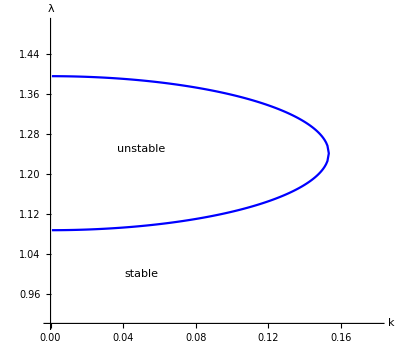

```mathematica
ListPlot[{data10},Joined->True, PlotRange->{{0,0.18},{0.9,1.5}},PlotStyle->{{PointSize[0.015], Blue},{PointSize[0.015], Red},{PointSize[0.015], Cyan}}, AxesStyle->{Directive[Black,Thickness[0.004],Arrowheads[{0,0.05}]], Directive[Black,Thickness[0.004],Arrowheads[{0,0.05}]]},AxesLabel->{Style["k",FontSize->20,FontFamily->"Times New Roman"],Style["λ",FontSize->20,FontFamily->"Times New Roman"]},Epilog->{Text[Style[ "stable",Medium],{0.05,1}],Text[Style[ "unstable",Medium],{0.05,1.25}]}, AspectRatio->0.9]
```

```mathematica
temp2=bifGent/.{B->1, Subscript[J, m]->100, λ->1.1};
FindRoot[(temp2/.k->0.0001)==0,{γ,5.777}]
```

{γ→5.7796}

```mathematica
dat={{0.0001, 5.779599592828826}};
```

```mathematica
guess=5.779599592828826*1.01;
Do[kk=0.0001+(0.45-0.0001)*i/100; guess=γ/.FindRoot[(temp2/.k->kk)==0,{γ,guess}]; dat=Append[dat,{kk,guess}], {i,1,100}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
dat
```

{{0.0001,5.7796},{0.004599,5.77971},{0.009098,5.78004},{0.013597,5.78058},{0.018096,5.78134},{0.022595,5.78232},{0.027094,5.78351},{0.031593,5.78491},{0.036092,5.78654},{0.040591,5.78838},{0.04509,5.79043},{0.049589,5.79271},{0.054088,5.7952},{0.058587,5.79792},{0.063086,5.80085},{0.067585,5.804},{0.072084,5.80737},{0.076583,5.81097},{0.081082,5.81478},{0.085581,5.81882},{0.09008,5.82309},{0.094579,5.82758},{0.099078,5.83229},{0.103577,5.83723},{0.108076,5.8424},{0.112575,5.8478},{0.117074,5.85344},{0.121573,5.8593},{0.126072,5.8654},{0.130571,5.87173},{0.13507,5.8783},{0.139569,5.8851},{0.144068,5.89215},{0.148567,5.89943},{0.153066,5.90696},{0.157565,5.91474},{0.162064,5.92276},{0.166563,5.93102},{0.171062,5.93954},{0.175561,5.94831},{0.18006,5.95734},{0.184559,5.96662},{0.189058,5.97616},{0.193557,5.98597},{0.198056,5.99603},{0.202555,6.00637},{0.207054,6.01697},{0.211553,6.02784},{0.216052,6.03899},{0.220551,6.05041},{0.22505,6.06212},{0.229549,6.0741},{0.234048,6.08638},{0.238547,6.09894},{0.243046,6.11179},{0.247545,6.12494},{0.252044,6.13839},{0.256543,6.15214},{0.261042,6.1662},{0.265541,6.18057},{0.27004,6.19525},{0.274539,6.21025},{0.279038,6.22557},{0.283537,6.24122},{0.288036,6.2572},{0.292535,6.27351},{0.297034,6.29016},{0.301533,6.30716},{0.306032,6.32451},{0.310531,6.34221},{0.31503,6.36027},{0.319529,6.37869},{0.324028,6.39749},{0.328527,6.41666},{0.333026,6.43621},{0.337525,6.45615},{0.342024,6.47648},{0.346523,6.49721},{0.351022,6.51834},{0.355521,6.53989},{0.36002,6.56186},{0.364519,6.58425},{0.369018,6.60708},{0.373517,6.63035},{0.378016,6.65407},{0.382515,6.67824},{0.387014,6.70287},{0.391513,6.72798},{0.396012,6.75357},{0.400511,6.77965},{0.40501,6.80623},{0.409509,6.83332},{0.414008,6.86092},{0.418507,6.88905},{0.423006,6.91772},{0.427505,6.94694},{0.432004,6.97672},{0.436503,7.00706},{0.441002,7.03799},{0.445501,7.06951},{0.45,7.10164}}

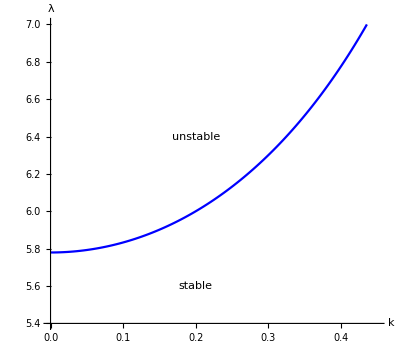

```mathematica
ListPlot[{dat},Joined->True, PlotRange->{{0,0.45},{5.4,7}},PlotStyle->{{PointSize[0.015], Blue},{PointSize[0.015], Red},{PointSize[0.015], Cyan}}, AxesStyle->{Directive[Black,Thickness[0.004],Arrowheads[{0,0.05}]], Directive[Black,Thickness[0.004],Arrowheads[{0,0.05}]]},AxesLabel->{Style["k",FontSize->20,FontFamily->"Times New Roman"],Style["λ",FontSize->20,FontFamily->"Times New Roman"]},Epilog->{Text[Style[ "stable",Medium],{0.2,5.6}],Text[Style[ "unstable",Medium],{0.2,6.4}]}, AspectRatio->0.9]
```

```mathematica
gg=Simplify[Simplify[Series[bif, {k,0,2}]]];
```

```mathematica
kk=Simplify[Coefficient[gg, k^2]/.{q1^2->q1s, q2^2->q2s}];
```

```mathematica
γgeneral=γ/.Simplify[Solve[kk==0, γ]][[1]]   (* this is γ when bifurcatoin takes place *)
```

(4 B w_d (λ (2+λ^3)+2 (-1+λ^3)^2 ω_1))/λ^(5/2)

```mathematica
γGent=Simplify[γgeneral/.{Subscript[w, d]->wdGent, Subscript[ω, 1]->wddGent/wdGent}](* this is γ for the Gent model when bifurcatoin takes place *)
```

(2 B J_m (-2+6 λ-8 λ^3+3 λ^4+λ^6+λ (2+λ^3) J_m))/(√λ (2-3 λ+λ^3-λ J_m)^2)

```mathematica
γHook=Limit[γGent, Subscript[J, m]->Infinity](* this is γ for the neo-Hookean model when bifurcatoin takes place *)
```

(4 B λ+2 B λ^4)/λ^(5/2)

```mathematica
F=2 λ wf'[(2+λ^3)/λ]-2 λ^-2 wf'[(2+λ^3)/λ]+γ/(λ^(1/2) B);
```

```mathematica
Simplify[Solve[D[F, λ]==0, γ]]
```

{{γ→(4 B (λ (2+λ^3) wf'[(2+λ^3)/λ]+2 (-1+λ^3)^2 wf''[(2+λ^3)/λ]))/λ^(5/2)}}

```mathematica
fg=D[γGent/.Subscript[J, m]->97.2/.B->1,λ];ssub=FindRoot[fg==0,{λ,1.2}]
```

{λ→1.23285}

```mathematica
γGent/.Subscript[J, m]->97.2/.B->1/.ssub
```

5.68682

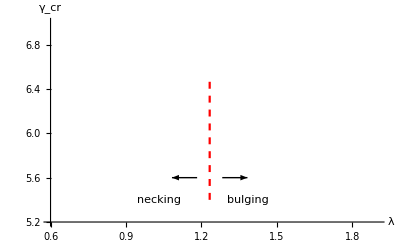

```mathematica
fig3a=ListPlot[{{1.23285, 5.4},{1.23285, 6.5}},Joined->True, AxesOrigin->{0.6, 5.2},  PlotRange->{{0.6, 1.9},{5.2,7}},PlotStyle->{{PointSize[0.015], Red, Dashed},{PointSize[0.015], Red},{PointSize[0.015], Cyan}}, AxesStyle->{Directive[Black,Thickness[0.004],Arrowheads[{0,0.05}]], Directive[Black,Thickness[0.004],Arrowheads[{0,0.05}]]},AxesLabel->{Style["λ",FontSize->20,FontFamily->"Times New Roman"],Style["γ_cr",FontSize->20,FontFamily->"Times New Roman"]}, Epilog->{Arrow[{{1.2328495568599604-0.05,5.6},{1.2328495568599604-0.15,5.6}}],Arrow[{{1.2328495568599604+0.05,5.6},{1.2328495568599604+0.15,5.6}}],Text[Style[ "necking",Medium],{1.2328495568599604-0.2,5.4}],Text[Style[ "bulging",Medium],{1.2328495568599604+0.15,5.4}]}]
```

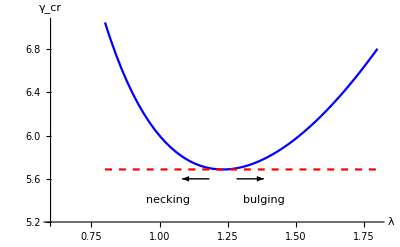

```mathematica
fig3b=Plot[{γGent/.Subscript[J, m]->97.2/.B->1, 5.68682218491149},{λ,0.8, 1.8},AxesOrigin->{0.6, 5.2}, PlotStyle->{{PointSize[0.015], Blue},{PointSize[0.015], Dashed, Red},{PointSize[0.015], Cyan}}, AxesStyle->{Directive[Black,Thickness[0.004],Arrowheads[{0,0.05}]], Directive[Black,Thickness[0.004],Arrowheads[{0,0.05}]]},AxesLabel->{Style["λ",FontSize->20,FontFamily->"Times New Roman"],Style["γ_cr",FontSize->20,FontFamily->"Times New Roman"]},Epilog->{Arrow[{{1.2328495568599604-0.05,5.6},{1.2328495568599604-0.15,5.6}}],Arrow[{{1.2328495568599604+0.05,5.6},{1.2328495568599604+0.15,5.6}}],Text[Style[ "necking",Medium],{1.2328495568599604-0.2,5.4}],Text[Style[ "bulging",Medium],{1.2328495568599604+0.15,5.4}]}]
```

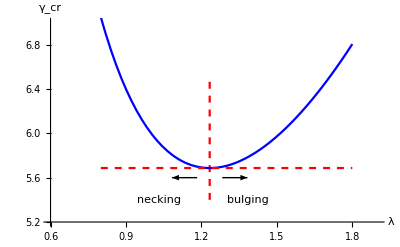

```mathematica
Show[fig3a,fig3b]
```